```mathematica
(*求f(x)=x的积分*)
```

```mathematica
Δx=(b-a)/n;Subscript[S, n]=n a Δx+(n (n+1))/2(Δx)^2;Limit[Subscript[S, n],n->Infinity]
```

1/2 (-a^2+b^2)

```mathematica
(*求f(x)=x^2 的积分*)
```

```mathematica
Δx = b / n; f[Subscript[_x, j]]=j^2 Δx^2;Subscript[S, n]=Sum[j^2 Δx^2 Δx,{j,1,n}];Limit[Subscript[S, n],n->Infinity]
```

b^3/3

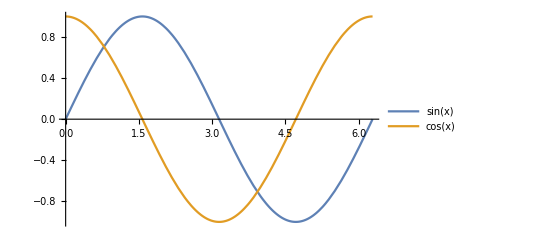

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2 Pi}, PlotLegends->"Expressions"]
```

```mathematica
D[Sin[x],x]
```

Cos[x]

```mathematica
D[Cos[x],x]
```

-Sin[x]

```mathematica
D[Tan[x], x]
```

Sec[x]^2

```mathematica
D[Cot[x],x]
```

-Csc[x]^2

```mathematica
∑_(i=1)^10 i
```

55

```mathematica
N[∑_(i=1)^10000 (-1)^(i-1)/(2 i - 1),3] 4
```

3.14

```mathematica
∫_1^x 1/u ⅆu
```

ConditionalExpression[Log[x],Re[x]>0||x∉ℝ]

```mathematica
D[x^n, x]
```

n x^(-1+n)

```mathematica
D[x^-1, x]
```

-1/x^2

```mathematica
Limit[∑_(j=1)^n (b/n)^(k+1)j^k,n->∞]
```

ConditionalExpression[b^(1+k)/(1+k),b^(1+k)∈ℝ&&k>0]

```mathematica
∑_(j=1)^∞ (b/n)^(k+1)j^k
```

(b (b/n)^k Zeta[-k])/n

```mathematica
∑_(i=1)^n i^k
```

HarmonicNumber[n,-k]

```mathematica
∑_(i=1)^∞ (-1)^(i+1)/i
```

Log[2]